Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2023/24
F.Javier Muñoz Delgado

# Notas y Prácticas 9: Ecuaciones diferenciales

## Ecuaciones diferenciales

## Repaso teórico Hallar la solución de una ecuación diferencial. Hallar la solución de un problema de valores iniciales. Resonancia. Problemas de exámenes. Problemas propuestos

## Repaso teórico

En ocasiones, buscamos una función a partir de una propiedad. Por ejemplo, si estudiamos el crecimiento de una población, P(t), a partir de los porcentajes de nacimientos y fallecimientos, tendremos que P’(t)=k P(t), donde k es la diferencia entre los dos porcentajes. Ahora se trata de buscar una función que cumpla esa condición. Este es una ejemplo de ecuación diferencial.

(La palabra ecuación hace referencia a una igualdad, donde hay algo desconocido y que nos plantea el reto de encontrarlo. También, en una ecuación, siempre tenemos la posibilidad de comprobar si una posible solución encontrada, es realmente una solución; basta sustituir en la ecuación y ver si la convierte en una identidad.)   

	Una ecuación diferencial es una ecuación que involucra a una función desconocida y a una o más de sus derivadas. Cuando la función desconocida dependa de una o más variables entonces las derivadas que aparecen en la ecuación diferencial serán derivadas parciales, y en este caso, se dice que es una ecuación en derivadas parciales. Si la función desconocida sólo depende de una variable independiente, las ecuaciones diferenciales reciben el nombre de ecuaciones diferenciales ordinarias.
	El orden de la ecuación diferencial es el orden de la derivada más alta de la ecuación diferencial.
En las ecuaciones diferenciales la función incógnita suele denotarse por alguna de la letras x, y, z, etc., mientras que las variables independientes por x, t, etc. Lo que siempre debe quedar claro es la función que queremos encontrar, sea y(x), y(t), x(t), etc.
Una ecuación diferencial ordinaria de orden n se representa en la forma
	F(t, x, (d x)/(d t), ..., (d^n x)/dt^n)=0
aunque, normalmente, se supondrá que es posible resolverla en la derivada n-ésima (es decir, despejar la derivada n-ésima), de modo que podamos expresarla en la forma explícita o normal
	
	x^(n))=G(t, x, x', ..., x^(n-1)))
	
Solución de una ecuación diferencial
Decimos que la función y = φ(x) es solución de la ecuación diferencial

                                F(x, y, y', ... , y^(n)) = 0
si se cumple que

                           F(x, φ(x), φ'(x), ... , φ^(n)(x)) = 0
                           
es decir, si al sustituir la función y = φ(x) en la ecuación diferencial se obtiene una identidad.
	El proceso de determinar todas las funciones que son soluciones de una ecuación diferencial se llama resolver o integrar la ecuación diferencial.
Usualmente, la resolución de una ecuación diferencial de orden n nos proporciona una familia n - paramétrica de soluciones o curvas integrales, que llamamos solución general. En este caso, para encontrar soluciones particulares bastaría dar valores a los parámetros.

Ejemplo:
	y’’ + 4 y = 0 es una ecuación diferencial de segundo orden. La función y(x)=cos 2x es una solución de la ecuación diferencial. También son soluciones las funciones y(x) = A cos 2x y B sen 2x, para A y B dos números reales cuales quiera.  
	
Problema de valores iniciales
	En muchas ocasiones no es necesario encontrar todas las soluciones de la ecuación diferencial sino una que cumpla ciertas condiciones. Usualmente del tipo valor de la función y de sus derivadas consecutivas (hasta un orden menos que la ecuación) en un punto. Estas condiciones se llaman condiciones iniciales y el problema de hallar una solución de la ecuación diferencial que además cumpla las condiciones iniciales se llama problema de valores iniciales o de Cauchy. Por ejemplo,

{x'=F(t,x)
x(t_0)=x_0

En otras ocasiones, a la ecuación diferencial se le añade unas condiciones en los extremos de un intervalo. En este caso, se denomina problema de valores en la frontera.  Por ejemplo,

{y''+ y=0
y(0)=y(π)=0

Ejemplo:
	y’ = 4 y 
	y(0)=100
es un problema de valores iniciales. La función y(x)=100 e^(4x) es una solución del problema, pues además de ser solución de la ecuación diferencial, cumple la condición inicial.

Existencia y unicidad
Dado el problema de valores iniciales (PVI)

{y'=F(x,y)
y(x_0)=y_0

si F es continua, existe al menos una solución del PVI definida en un intervalo abierto que contiene al punto x_0. Además, si tanto F como ∂_y F son continuas en un entorno del punto (x_0,y_0) entonces existe una única solución en un intervalo abierto que contenga al punto x_0.

Ejemplo de Problema de valores iniciales donde no hay unicidad.
									{y'=2 √y
y(0)=0
Todas las funciones de la forma f_a(x)=(x-a)_+^2={0, si x<a
(x-a)^2, si x ≥a	con a≥0, son soluciones de la ecuación. Para comprobarlo basta calcular la derivada de estas funciones	
f_a'(x)={0, si x<a
2(x-a), si x ≥a	y sustituir en la ecuación diferencial. Además, cumplen la condición inicial al valer 0 en el punto.

La función F(x,y)=√y y su derivada, ∂_y F=1/(√y), no son funciones continuas en un entorno del punto (0,0), por tanto no podríamos usar el teorema que garantiza la existencia y unicidad.					

Comando DSolve (I)
Mathematica dispone del comando DSolve para hallar la expresión simbólica de la solución de una ecuación diferencial. Su sintaxis es:

DSolve[ y'[x] == f [x, y[x] ], y[x], x]

donde y'[x] == f [x, y[x] ] es la ecuación diferencial que intentamos resolver, en la que y es una función de la variable independiente x. 
Para incluir las condiciones iniciales emplearemos la notación:

DSolve[{ ecuación, condición1, condición2, ... }, y[x], x]

donde ecuación es la ecuación que se va a resolver, en la que y es una función de la variable independiente x.

Con el Mathematica podemos resolver ecuaciones diferenciales. Utilizamos la instrucción DSolve

```mathematica
DSolve[y'[x]==2y[x],y[x],x]
```

{{y[x]→ⅇ^(2 x) C[1]}}

La solución general de la ecuación diferencial y’=2y es y(x) = C ⅇ^(2x), con C una constante real cualquiera. Hay infinitas soluciones. También podemos resolver Problemas de Valores Iniciales.

```mathematica
DSolve[{y'[x]==2y[x],y[0]==1000},y[x],x]
```

{{y[x]→1000 ⅇ^(2 x)}}

Ahora tenemos la solución del problema de valores iniciales y’=2y, y(0)=1000. 
Se trata de la función y(x) = 1000 ⅇ^(2x).

#### Tipos de ecuaciones diferenciales estudiadas: 1) Integrales (y’=f(x)), 2) y’=ay 3) y’=f(x) y 4) y’=f(x)g(y) 5) a_n y^(n))+a_(n-1) y^(n-1))+...+a_1 y'+a_0 y =0 6) a_n y^(n))+a_(n-1) y^(n-1))+...+a_1 y'+a_0 y =f(x) 7) Sistemas de ecuaciones diferenciales lineales x’=ax+by y’=cx +dy 1) y(x)=∫f(x)ⅆx + C, C∈ ℝ 2) y(x)=0 es solución. Si y(x)≠0, despejamos y’(x) / y(x) = a, e integramos: ∫y'(x)/y(x)ⅆx = ∫aⅆx. Entonces, Log |y(x)|=ax+c, con c un número real cualquiera. Usando exponenciales, |y(x)|=ⅇ^(ax+c)=ⅇ^axⅇ^c; y(x)=±ⅇ^c ⅇ^ax. Finalmente, podríamos escribir y(x)= C ⅇ^ax, C∈ ℝ. 3) De forma similar, y(x)=0 es solución. Si y(x)≠0, despejamos y’(x) / y(x) = f(x), e integramos: ∫y'(x)/y(x)ⅆx = ∫f(x)ⅆx. Entonces, Log |y(x)|=∫f(x)ⅆx+c, con c un número real cualquiera. Usando exponenciales, |y(x)|=ⅇ^(∫f(x)ⅆx+c)=ⅇ^(∫f(x)ⅆx)ⅇ^c; y(x)=±ⅇ^c ⅇ^(∫f(x)ⅆx). Finalmente, podríamos escribir y(x)= C ⅇ^(∫f(x)ⅆx), C∈ ℝ. 4) Una forma usual de escribir las derivadas es la siguiente: y’(x)=dy/dx. Así, la ecuación y’=f(x)g(y), se podría escribir como dy/dx=f(x)g(y), y es fácil encontrar en libros: dy = f(x) g(y) dx, ó dy/(g(y))=f(x)dx. A continuación se hace integral en cada término: ∫1/(g(y))ⅆy = ∫f(x)ⅆx. Tras calcular las integrales podríamos encontrar y(x). Es posible que no podamos despejar y(x), así tendríamos la solución de forma implícita. 5) Para resolver la ecuación diferencial: a_n y^(n))+a_(n-1) y^(n-1))+...+a_1 y'+a_0 y =0, podemos plantearnos si hay alguna solución del tipo y(x)= ⅇ^ax. Para que fuese solución tendría que cumplirse la ecuación diferencial, es decir al sustituir en la ecuación diferencial deberíamos encontrar una identidad. a_n a^n ⅇ^ax+a_(n-1) a^(n-1)ⅇ^ax+...+a_1 a ⅇ^ax+a_0 ⅇ^ax =0 Sacando factor común ⅇ^ax, tenemos ⅇ^ax( a_n a^n + a_(n-1) a^(n-1)+ ... + a_1 a +a_0 ) =0. Como la exponencial no es cero, debería serlo (a_n a^n + a_(n-1) a^(n-1)+ ... + a_1 a +a_0 ), por tanto a debería ser solución de la ecuación polinómica a_n x^n + a_(n-1) x^(n-1)+ ... + a_1 x +a_0 =0. Por ello, cuando tenemos una ecuación diferencial a_n y^(n))+a_(n-1) y^(n-1))+...+a_1 y'+a_0 y =0 le asociamos una ecuación polinómica: a_n x^n+a_(n-1) x^(n-1) +...+a_1 x+a_0 = 0 Si las soluciones de la ecuación polinómica son los n números reales distintos: r_1, r_2, r_3, ..., r_n, la solución general de la ecuación diferencial y(x)= C_1 ⅇ^(r_1 x)+ C_2 ⅇ^(r_2 x)+ ...+ C_n ⅇ^(r_n x), con C_1, C_2, ..., C_n ∈ ℝ. Cabe la posibilidad de que la ecuación polinómica tenga raíces complejas conjugadas, a ± b ⅈ, en ese caso, recordando la exponencial de números complejos, las soluciones asociadas serían ⅇ^ax cos(bx) y ⅇ^ax sen(bx). Otra posibilidad es que alguna raíz del polinomio, r, sea múltiple. Si la raíz tiene multiplicidad m, además, de la solución asociada, tenemos m-1 soluciones más, que consisten en multiplicar por x, x^2, x^3, ..., x^(m-1). 6) Para resolver la ecuación diferencial lineal con coeficientes constantes completa, a_n y^(n))+a_(n-1) y^(n-1))+...+a_1 y'+a_0 y = f(x), primero consideramos la ecuación homogénea a_n y^(n))+a_(n-1) y^(n-1))+...+a_1 y'+a_0 y = 0 y encontramos su solución general (según lo visto en 5)). A continuación, el método que estudiamos es observar el tipo de función que es f(x). Si f(x), es una constante, un polinomio de grado m, una función seno o coseno, una función exponencial, (o una suma de esos tipos), probaríamos con funciones similares, dejando libres ciertas constantes que obtendremos al imponer que sea solución de la ecuación diferencial completa. Si f(x) = a, una constante, probamos con y_p(x)= α. Calculamos el valor de α para que sea solución. Si f(x) = a x^m+b x^(m-1) +...+ c x + d, probamos con y_p(x)= α x^m+β x^(m-1) +...+ γ x + δ, encontrando los valores de α, β, ..., γ, δ. Si f(x) = a cos bx, o f(x) = a sen bx, probamos con y_p(x)= α cos bx + β cos bx Si f(x) = a ⅇ^bx, probamos con y_p(x)= α ⅇ^bx Si la función que aparece en f(x) es una solución de la ecuación diferencial homogénea, tendremos (como pasa cuando hay raíces múltiples) que multiplicar por x, o potencias de x, de forma que la función/es con la que probemos no sea solución de la ecuación homogénea. Una vez que encontremos una solución particular de la ecuación diferencial completa, sumamos esa solución con la solución general de la ecuación diferencial homogénea. 7) Dado un sistema de ecuaciones, x’=ax+by y’=cx +dy donde debemos encontrar las funciones x(t) e y(t), podemos resolverlo, despejando y derivando, llegando a una ecuación con una sola de las funciones: x’’=ax’+by’=ax’+b(cx+dy)=ax’+bcx+bdy=ax’+bcx+d(x’-ax)=(a+d)x’+(bc-ad)x Una vez calculada x, calcularíamos y. Si x(t) e y(t) representan los individuos de dos grupos, el signo de los coeficientes puede representar la relación entre ambos colectivos, si colaboran, si compiten, si uno actúa como presa y otro como depredador, etc. También podemos resolver sistemas de ecuaciones un poco más generales x’=ax+by+c y’=dx +ey+f De nuevo, despejando y derivando, podemos llegar a una ecuación con una sola de las funciones: x’’=ax’+by’=ax’+b(dx+ey+f)=ax’+bdx+bey+bf=ax’+bdx+e(x’-ax-c)+bf=(a+e)x’+(bd-ae)x-ec+bf Ahora tendremos una ecuación diferencial de segundo orden con coeficientes constantes completa: x’’-(a+e)x’-(bd-ae)x = -ec+bf Una vez calculada x(t), calcularíamos y(t) =(x’(t)-a x(t)-c)/b. MUY IMPORTANTE: En cualquier momento, al finalizar el problema, o durante la resolución de un problema, podemos comprobar si la función encontrada es la solución de la ecuación diferencial. El concepto de solución de una ecuación es muy importante. No es necesario repasar los cálculos realizados, suele ser más eficaz comprobar si al sustituir la función en la ecuación, esta se convierte en una identidad. Ejemplos resueltos con el Mathematica:

```mathematica
DSolve[y'[x]==x Cos[x],y[x],x]
```

{{y[x]→C[1]+Cos[x]+x Sin[x]}}

```mathematica
DSolve[y'[x]==3 y[x],y[x],x]
```

{{y[x]→ⅇ^(3 x) C[1]}}

```mathematica
DSolve[y'[x]==x y[x],y[x],x]
```

{{y[x]→ⅇ^(x^2/2) C[1]}}

```mathematica
DSolve[y'[x]==Cos[x] Cos[y[x]],y[x],x]
```

{{y[x]→2 ArcTan[Tanh[1/4 (C[1]+2 Sin[x])]]}}

```mathematica
DSolve[y''[x]-y'[x]-2y[x]==0,y[x],x]
```

{{y[x]→ⅇ^-x C[1]+ⅇ^(2 x) C[2]}}

```mathematica
DSolve[y''[x]-y'[x]-2y[x]==2+x,y[x],x]
```

{{y[x]→1/4 (-3-2 x)+ⅇ^-x C[1]+ⅇ^(2 x) C[2]}}

#### Problema del enfriamiento del café. Suponemos la ley de enfriamiento de Newton, y’=K(M-y), donde M es la temperatura del medio ambiente, K una constante que depende de cómo se pierde el calor e y(x) la temperatura del café en el momento x. Supongamos que M=20 grados, y(0)=80 e y(1)=70, encontrar y(x). ¿Cuándo y(x)=35 o y(x)=25?

Solución:
Podemos pedir al Mathematica que resuelva la ecuación diferencial:

```mathematica
DSolve[y'[x]==k (20-y[x]),y[x],x]
```

{{y[x]→20+ⅇ^(-k x) C[1]}}

Otra posibilidad, más rápida, es pedir que resuelva la ecuación y la condición inicial:

```mathematica
DSolve[{y'[x]==k (20-y[x]),y[0]==80},y[x],x]
```

{{y[x]→20 ⅇ^(-k x) (3+ⅇ^(k x))}}

```mathematica
y[x_]:= 20 ⅇ^(-k x) (3+ⅇ^(k x))
```

Aquí no conocemos el valor de k, pues dependerá de diversas cuestiones como el aislamiento del recipiente, de la velocidad del aire, etc. Para salvar este problema, usamos una segunda medición de la temperatura al minuto.

```mathematica
Solve[y[1]==70,k,Reals]
```

{{k→Log[2]+Log[3]-Log[5]}}

```mathematica
k=Log[2]+Log[3]-Log[5];
```

Al imponer que la temperatura al minuto sea de 70 grados, obtenemos el valor de k.

```mathematica
y[x]
```

20 ⅇ^(x (-Log[2]-Log[3]+Log[5])) (3+ⅇ^(x (Log[2]+Log[3]-Log[5])))

```mathematica
Solve[y[x]==35,x,Reals]//N
```

{{x→7.60357}}

La temperatura bajará hasta los 35 grados en 7.6 minutos.

```mathematica
Solve[y[x]==25,x,Reals]//N
```

{{x→13.6293}}

La temperatura bajará hasta los 25 grados en 13.6 minutos.

```mathematica
Clear[y]
```

#### Depreciación de un vehículo Supongamos que el precio de un vehículo, P(t), se deprecia un 10% anual y que cada año se le realizan tareas de mantenimiento por un importe de 300 euros. Si inicialmente el valor era de 30.000 euros, calcular, resolviendo la ecuación diferencial P’(t) = -0.1P(t)+300, la función P(t).

Solución:
Se trata de resolver el problema de valores iniciales:
P’ = -0.1 P+300
P(0)=30000

Comenzaremos resolviendo la ecuación diferencial, P’+0.1P = 300. Se trata de una ecuación diferencial de primer orden lineal con coeficientes constantes completa. Para resolverla, comenzamos con la homogénea:  P’+0.1P = 0.
Asociamos la ecuación algebraica (o polinómica): x+0.1=0. Su solución es x=-0.1.
La solución general de la ecuación diferencia homogénea es C e^(-0.1 t), con C número real cualquiera.

Para hallar una solución particular de la completa, y a la vista de que el término independiente es una constante, probaremos con constantes:
y(t)=k
Derivamos:	y’(t)=0
Sustituimos en la ecuación diferencial completa: 0+0.1 k=300. De donde obtenemos que k=3000. Por tanto, la solución particular de la completa es 3000.

La solución general de la completa sería la suma de ambas: P(t) = 3000 + C e^(-0.1 t), con C número real cualquiera.

Para resolver el problema de valores iniciales, imponemos la condición inicial y calculamos el valor de la constante C.
P(0) = 3000 + C e^(-0.1 *0) = 3000 + C = 30000, de donde C=27000.

La solución del problema de valores iniciales es P(t) = 3000 + 27000 e^(-0.1 t).

#### La resonancia Al estudiar la ecuaciones diferenciales lineales de grado superior con coeficientes constantes, consideramos primero la parte homogénea y luego buscamos una solución particular de la completa. Para buscar una solución de la completa, consideramos funciones similares a las que hay en el término independiente. Consideremos la ecuación y’’+y=0 con condiciones y(0)=0, y’(0)=1.

```mathematica
DSolve[y''[x]+y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

```mathematica
DSolve[{y''[x]+y[x]==0,y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→Sin[x]}}

La solución es la función seno (en realidad, las soluciones de la ecuación diferencial deben ser combinaciones lineales de las funciones seno y coseno. Al imponer las condiciones iniciales, aparece en este caso la función seno)

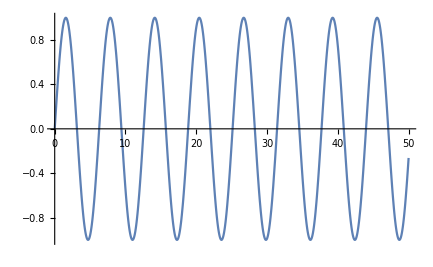

```mathematica
Plot[Sin[x],{x,0,50}]
```

Si introducimos una función en el término independiente, la solución se modifica.

```mathematica
DSolve[{y''[x]+y[x]==1,y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→1-Cos[x]+Sin[x]}}

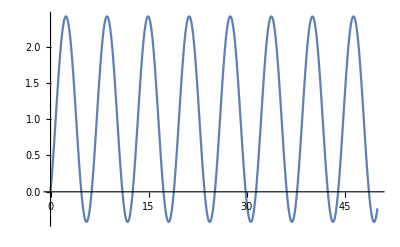

```mathematica
Plot[1-Cos[x]+Sin[x],{x,0,50}]
```

Por ejemplo, al poner la función constante 1, la solución es 1-cos x + sen x. Se trata de una función “similar” a la inicial.

```mathematica
DSolve[y''[x]+y[x]== Cos[a x],y[x],x]//Simplify
```

{{y[x]→((-1+a^2) C[1] Cos[x]-Cos[a x]+(-1+a^2) C[2] Sin[x])/(-1+a^2)}}

Si ponemos como término independiente cos(ax) la solución es similar, salvo que a sea 1 o -1. Recordemos que si el término independiente es cos(ax) probaríamos con funciones del tipo A cos(ax) + B sen(ax), salvo que a sea 1 o -1, pues debemos probar con funciones del tipo  Ax cos(ax) + Bx sen(ax). En este caso, las soluciones no serían acotadas.

```mathematica
DSolve[{y''[x]+y[x]==Cos[a x]/20,y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→1/(2 (-1+a^2))(Cos[x]-Cos[x]^2 Cos[a x]-2 Sin[x]+2 a^2 Sin[x]-Cos[a x] Sin[x]^2)}}

Cuando a = 1 es cuando deja de estar acotada porque es cuando el término independiente se parece a la solución. Es una solución de la homogénea. Sería la mejor forma de “empujar al columpio” o al muelle para que oscile más. No es importante que el término independiente sea muy grande o no ( de hecho al dividirlo por 20, sigue ocurriendo lo mismo. Si a es distinto de 1 o -1, no hay mucha diferencia. Si a es 1 o -1, aparece una solución no acotada.)

Este fenómeno se llama de resonancia. Con una fuerza “pequeña”, pero con una frecuencia adecuada se consiguen cosas “sorprendentes”; copas de cristal que se rompen con la voz, puentes que se caen por el viento o al desfilar los soldados, columpios, los receptores de radio, etc. En todos ellos, lo importante es que la fuerza se produzca con la frecuencia adecuada.

```mathematica
Manipulate[Plot[1/(2 (-1+a^2))(Cos[x]-Cos[x]^2 Cos[a x]-2 Sin[x]+2 a^2 Sin[x]-Cos[a x] Sin[x]^2),{x,0,50}],{a,0,2}]
```

Mientras el parámetro a está lejos del 1, la solución es “similar”; funciones acotadas. Cuando a se acerca al 1, la función empieza a tomar valores mayores y aparecen funciones no acotadas.

Problemas de exámenes.

## 9.- Resolver la ecuación diferencial y’’ - 4y = 4 t^2 + 2. Enero 2018

Solución:
Se trata de una ecuación diferencial lineal con coeficientes constantes de segundo orden completa. Para encontrar sus soluciones comenzamos estudiando la ecuación diferencial homogénea asociada; y’’ - 4y = 0. Para resolverla consideramos la ecuación polinómica asociada X^2-4=0.  Las soluciones de esta ecuación son 2 y -2. Por tanto, la solución general de la ecuación diferencial homogénea es y_h(t) = C_1 ⅇ^(2t) + C_2 ⅇ^(-2t), donde C_1 y C_2 son dos constantes reales cualesquiera.

Una vez resuelta la homogénea, pasamos a estudiar la ecuación completa y buscar una solución particular. Dado que el término independiente es un polinomio de segundo grado, intentamos encontrar una solución que sea un polinomio de segundo grado:
	y_p(t) = A t^2+ B t + C
Derivamos
	y_p'(t) = 2A t + B
	y_p’’(t) = 2A
Sustituimos
	y_p’’ - 4y_p = 2A - 4(A t^2+ B t + C) = - 4A t^2- 4 B t + 2A-4C = 4 t^2 + 2.
Igualando los coeficientes de las potencias de t, obtenemos -4A=4, -4B=0, 2A-4C=2. Por tanto, A=-1, B=0, C=-1.
La solución particular es y_p(t) = - t^2-1.
La solución general de la ecuación diferencial completa es la suma de la solución general de la homogénea y la particular de la completa.
	y(t)= - t^2-1 + C_1 ⅇ^(2t) + C_2 ⅇ^(-2t), donde C_1 y C_2 son dos constantes reales cualesquiera

## 2.- Una sustancia radiactiva se está desintegrando según la ecuación diferencial y’= - K y, para una cierta constante K sabiendo que y(0)=40 e y(2)=20, calcular y(5). Enero 2018. Aula de informática

Solución: La solución de la ecuación diferencial y’=-K y es y(x)= C ⅇ^-Kx con C número real. Imponiendo que y(0) sea 40, tenemos que C=40. Como y(2) debe ser 20 tenemos que y(2)= 40 ⅇ^(-2K) = 20. Despejamos: ⅇ^(-2K)=1/2. Tomamos logaritmos, -2K = log(1/2). K= (-ln(1/2))/2. Por tanto, y(x)= 40 ⅇ^-Kx = 40 (1/2)^(x/2). Evaluando en x=5, y(5)=40 (1/2)^(5/2)=5√2

## 8.- Resolver la ecuación diferencial y’ - y = x + e^x. Julio 2018

Solución:
Se trata de una ecuación diferencial lineal con coeficientes constantes de primer orden completa. Para encontrar sus soluciones comenzamos estudiando la ecuación diferencial homogénea asociada; y’ - y = 0. Para resolverla consideramos la ecuación polinómica asociada X-1=0.  La solución de esta ecuación 1. Por tanto, la solución general de la ecuación diferencial homogénea es y_h(x) = C_1 ⅇ^x  donde C_1 es una constante real cualesquiera.

Una vez resuelta la homogénea, pasamos a estudiar la ecuación completa y buscar una solución particular. Dado que el término independiente es una suma de polinomio de primer grado y exponencial, intentamos encontrar una solución que sea suma de polinomio de primer grado y exponencial. Vemos también que ⅇ^x es solución de la homogénea. Por ello, probamos con funciones del tipo:
	y_p(x) = A x ⅇ^x+ B x + C
Derivamos
	y_p'(x) = A ⅇ^x + A x ⅇ^x+ B
Sustituimos
	y_p’ - y_p = A ⅇ^x + A x ⅇ^x+ B -  (A x ⅇ^x+ B x + C) = A ⅇ^x +  B -  B x - C 

que debe ser igual a  x +  ⅇ^x 
Igualando,  
A ⅇ^x +  B -  B x - C  = x +  ⅇ^x 

A debe ser 1, B debe ser -1 y C debe ser igual a B. 

Por tanto, A=1, B=-1, C=-1.

La solución particular es y_p(x) = x ⅇ^x - x -1
La solución general de la ecuación diferencial completa es la suma de la solución general de la homogénea y la particular de la completa.
	y(x) = x ⅇ^x - x -1 + C_1 ⅇ^x , donde C_1 es una constante real cualquiera.
Con el Mathematica podemos comprobar también la solución.

```mathematica
DSolve[y'[x]-y[x]==x+ⅇ^x,y[x],x]//Simplify
```

{{y[x]→-1+(-1+ⅇ^x) x+ⅇ^x C[1]}}

## 2.- Dado el problema de valores iniciales y’ = 2 y (20-y) con y(G)=M, escribir y(G+1) con 8 cifras decimales. (G y M son ciertas cifras de vuestro DNI) Julio 2018. Aula de informática

Solución:
Supongamos G=3, M=5:

```mathematica
DSolve[y'[x]==2y[x](20-y[x]),y[x],x]
```

{{y[x]→(20 ⅇ^(40 x))/(ⅇ^(40 x)+ⅇ^(20 C[1]))}}

```mathematica
DSolve[{y'[x]==2y[x](20-y[x]),y[3]==5},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→(20 ⅇ^(40 x))/(3 ⅇ^120+ⅇ^(40 x))}}

```mathematica
(20 ⅇ^(40 x))/(3 ⅇ^120+ⅇ^(40 x))/.{x->4}
```

(20 ⅇ^160)/(3 ⅇ^120+ⅇ^160)

```mathematica
Simplify[%]
```

(20 ⅇ^40)/(3+ⅇ^40)

## 8.- Resolver la ecuación diferencial y’ - y = x - e^x. Octubre 2018. Aula de informática

## Enero 2019. 9.- Calcular el valor de a para que la función y(x)=1/(1+ax) sea solución de la ecuación diferencial y’ = y^2.

Solución:
Para que la función y(x) sea solución necesitamos que cumpla la ecuación diferencial. Por tanto,
		y’(x) = -a/(1+a x)^2 = (y(x))^2= 1/(1+a x)^2
De donde obtenemos a=-1.

## 2.- Dado el problema de valores iniciales y’ = 2 y (20-y) con y(0)=1, escribir y(0.1) con 8 cifras decimales. Enero 2019. Aula de informática

Solución: Resolvemos con el Mathematica la ecuación diferencial con la condición inicial:

```mathematica
DSolve[{y'[x]==2 y[x](20-y[x]),y[0]==1},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→(20 ⅇ^(40 x))/(19+ⅇ^(40 x))}}

```mathematica
N[(20 ⅇ^4)/(19+ⅇ^4),10]
```

14.83682674

## 2.- La temperatura de un cuerpo que se está enfriando se aproxima por la solución de la ecuación diferencial y’= K (20-y), para una cierta constante K, sabiendo que y(0)=40 e y(2)=30, calcular y(5). Aula de informática

Solución: Resolvemos con el Mathematica la ecuación diferencial con una condición inicial:

```mathematica
DSolve[{y'[x]==k (20-y[x]),y[0]==40},y[x],x]
```

{{y[x]→20 ⅇ^(-k x) (1+ⅇ^(k x))}}

Ahora calculamos k, sabiendo que en x=2 la función vale 30. 
		30 = 20 ⅇ^(-2k) (1+ⅇ^(2k))=20 ⅇ^(-2k) +20;
		10= 20 ⅇ^(-2k); -2k = log (1/2) ; k = - log(1/2)/2=log(2)/2
Con lo cual, y(5)= 20 ⅇ^(-5k) (1+ⅇ^(5k))= 20 ⅇ^(-5k)+20 = 20 + 20  ⅇ^(-5log (2)/2)= 20 + 20*2^(-5/2), aproximadamente 23,5355

```mathematica
Solve[20 ⅇ^(-2k) (1+ⅇ^(2k))==30,k]
```

{{k→ConditionalExpression[1/2 (2 ⅈ π C[1]+Log[2]),C[1]∈Integers]}}

```mathematica
k=1/2 (Log[2])
```

Log[2]/2

```mathematica
20 ⅇ^(-k x) (1+ⅇ^(k x))/.x->5//Simplify
```

5/2 (8+√2)

```mathematica
N[%]
```

23.5355

## 8.- Resolver la ecuación diferencial y’’ + 2y’ - 3y = 10 e^(2 t). Enero 2020

Solución: Comenzamos con la ecuación homogénea: y’’ + 2y’ - 3y =0. 
Buscamos las raíces del polinomio asociado: x^2+2x-3=0=(x+3)(x-1), x=1, -3. 
La solución general de la homogénea es y_h(t)=C_1 e^t+C_2 e^(-3 t).
Ahora buscamos una solución particular de la completa del mismo tipo que el término independiente, es decir una exponencial de 2t;
y_p(t)=C e^(2t).
De donde y'_p(t)= 2C e^(2t), y''_p(t)=4C e^(2t)
Sustituimos en la ecuación diferencial: 
4C e^(2t) + 4C e^(2t)- 3C e^(2t) = 10 e^(2 t), de donde 5C e^(2t) = 10 e^(2t) , por tanto C=2.

La solución general de la completa es y_c(t) = 2 e^(2 t)+C_1 e^t+C_2e^(-3 t).

## 2.- Determinar los valores del parámetro m para los que la función h(x) = x^m es una solución de la ecuación diferencial x^2y’’ - 7xy’ + 15 y = 0. Enero 2020. Aula de Informática

Se podría sustituir en la ecuación la función h(x)=x^m y encontrar cuándo es solución:
Si h(x) =x^m, h’(x)= m x^(m-1), h’’(x)=m(m-1) x^(m-2). (Los casos m=0 o 1, se pueden estudiar aparte)

x^2m(m-1) x^(m-2)  - 7xm x^(m-1) + 15 x^m = m(m-1) x^m  - 7m x^m + 15 x^m = (m(m-1)  - 7m + 15 )x^m=0 cuando  m(m-1)  - 7m + 15=0, resolviendo esta ecuación m^2  - 8m + 15=0, encontramos, m=5 ó 3. 

Otra posibilidad es, utilizando el Mathematica, resolver la ecuación de partida y ver las posibles soluciones.

```mathematica
DSolve[x^2 y''[x]-7 x y'[x] +15 y[x]==0,y[x],x]
```

{{y[x]→x^3 C[1]+x^5 C[2]}}

## 10.- Resolver la ecuación diferencial y’’ - y = 3 x^2-2x+1. Enero 2022

Solución:
Se trata de una ecuación diferencial lineal de coeficientes constantes completa. 
1) Se resuelve en primer lugar, la ecuación diferencial homogénea: y’’ - y = 0. 
	Para ello se resuelve la ecuación polinómica asociada: x^2 - 1 = 0; x^2 = 1;  x=± 1.
	Si las soluciones de la ecuación polinómica son 1 y -1, la solución general de la ecuación diferencial homogénea es:
	y_h(x) = C_1 ⅇ^x +  C_2 ⅇ^-x , con C_1 , C_2 números reales cualesquiera
2) A continuación se busca una solución particular de la ecuación diferencial completa: y’’ - y = 3 x^2 - 2x + 1.
	Nos fijamos en que el término independiente es un polinomio de grado 2. (Que no es solución de la ecuación homogénea.) Probaremos con una función del tipo  y_p(x) = a + b x + c x^2.
	y_p(x) = a + b x + c x^2
	y_p'(x) = b + 2 c x
	y_p''(x) = 2c
Ahora sustituimos en la ecuación diferencial:
	y_p'' - y_p = 2c  - (a + b x + c x^2) = 2c - a - b x - c x^2 = 3 x^2-2x+1
De donde -c=3, -b=-2, 2c-a= 1. Por tanto, c=-3, b=2, a=2c-1=-6-1=-7
	La solución particular es  y_p(x) = -7 +2x-3x^2.
La solución general es y(x) = -7+2x-3 x^2+C_1 ⅇ^x +  C_2 ⅇ^-x , con C_1 , C_2 números reales cualesquiera.

Con el Mathematica

```mathematica
DSolve[y''[x]-y[x]==3x^2-2x+1,y[x],x]
```

{{y[x]→-7+2 x-3 x^2+ⅇ^x C[1]+ⅇ^-x C[2]}}

## 9.- Resolver el problema de valores iniciales y’ = x y con la condición inicial y(0)=1. Julio 2022

Solución:

Tratamos primero de resolver la ecuación diferencial encontrando la solución general. Después impondremos la condición inicial y buscaremos la solución del problema de valores iniciales.
La ecuación diferencial y’ = x y es una ecuación diferencial de variables separadas. Podemos escribir y’ como dy/dx. Una solución fácil de encontrar es la función constante y(x)=0. Si y es distinto de cero,

dy/dx= x y ⟹ dy/y= x dx ⟹  ∫1/y ⅆy = ∫xⅆx ⟹ Log |y| = x^2/2  + C ⟹  |y| = e^(x^2/2+C)  = e^(x^2/2) e^C⟹ y = ±e^(x^2/2) e^C (la exponencial multiplicada por una constante diferente de cero) 
Uniendo con la solución cero, podemos escribir como solución general y(x) = K e^(x^2/2), con K un número real cualquiera.
Para encontrar la solución particular del problema de valores iniciales, imponemos la condición inicial y(0)=1,
y(0) = K e^(0^2/2) = K, por tanto K debe ser 1.
La solución del PVI es y(x) = e^(x^2/2).

## 10.- Resolver la ecuación diferencial y’ - y = 3 x^2 - 2x + 1. Julio 2022

Solución:
Se trata de una ecuación diferencial lineal de orden 1 con coeficientes constantes completa. 

Para resolverla, comenzamos por estudiar la ecuación homogénea, y’-y=0.
La ecuación algebraica asociada es x-1=0. La solución es x=1, por tanto, la solución general de la homogénea es yh(x) = C e^x.

Ahora consideramos la ecuación completa. El término independiente es un polinomio de grado 2, por ello vamos a buscar una solución particular que sea un polinomio de grado dos.
yp(x) = a x^2 + bx + c
yp’(x) = 2a x + b
Sustituimos en la ecuación diferencial yp’ - yp = (2ax+b)-(a x^2 + bx + c) = -a x^2 + (2a-b)x + b-c = 3 x^2 - 2x + 1.
De aquí obtenemos que -a=3, 2a-b=-2, b-c=1. Por tanto, a=-3, b=2+2a=2-6=-4, c=b-1=-4-1=-5.
La solución particular es yp(x)=-3 x^2 - 4x - 5. La solución general de la ecuación completa es y(x) =  C e^x- 3 x^2 - 4x - 5, con C un número real cualquiera.

## 2.- Supongamos que un café sale de la máquina a 80 grados y tras un minuto en una sala que se encuentra a 20 grados, la temperatura baja hasta los 70 grados. Suponemos la ley de enfriamiento de Newton, es decir, que la temperatura del café sigue la ecuación diferencial y’=K(M-y), donde M es la temperatura del medio ambiente, K una constante que depende de cómo se pierde el calor e y(x) la temperatura del café en el momento x. ¿Qué temperatura tendrá el café a los 3 minutos de salir de la máquina? 1) 44.1127, 2) 40.0939, 3) 48.9352, 4) 61.6667, 5) 54.7222 Enero 22. Aula de Informática

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{y'[x]==K(20-y[x]),y[0]==80},y[x],x]
```

{{y[x]→20 ⅇ^(-K x) (3+ⅇ^(K x))}}

```mathematica
y[x_]:=20 ⅇ^(-K x) (3+ⅇ^(K x))
```

```mathematica
Solve[y[1]==70,K,Reals]
```

{{K→Log[2]+Log[3]-Log[5]}}

```mathematica
y[3]/.%//N
```

{54.7222}

Relación. Ecuaciones Diferenciales Ordinarias

1.- Comprobar si las siguientes funciones constituyen soluciones de las ecuaciones diferenciales correspondientes: 
  
  	a ) y = x^2 + c , c∈ℝ		                            EDO: y’ = 2 x
  	b ) y = c_1 sen(2x) +  c_2 cos(2x),  c_1, c_2∈ℝ		EDO: y’’ + 4 y = 0
  	c) y = C e^(3 x) + 1 , con C∈ℝ			EDO: y’- 3 y +3= 0 
  	
  2.- Determinar los valores del parámetro m para los que la función h(x) = x^m es una solución de la ecuación diferencial x^2y’’  - 7xy’ + 15 y = 0. 
  
  3.- Demostrar que f(x) = sen(x) - cos(x) es una solución del PVI  
		y’’ + y = 0
		y(0) = -1
		y’ (0) = 1
  4.- Obtener la solución general de las siguientes ecuaciones diferenciales de primer orden de variables separables:
		▪ ( 1 + x ) dy - y dx = 0
		▪ (d y)/(d x) = (x + (1))^2
		▪ (d S)/(d t)= k S, k ∈ℝ
		▪ y’ = (x^2 y - y)/(y + 1)
		▪ (d P)/(d t)= P - P^2
		▪ y’ = e^(3 x + 2 y)
		▪ (d Q)/(d t)= k (Q -60), k ∈ℝ
		▪ (d N)/(d t)+ N = N t e^(t + 2)	
  5.- Obtener la solución general de las siguientes ecuaciones diferenciales lineales de primer orden:
	▪ y’(t) + 2ty = 0	
	▪ (d y)/(d t)+ y cos(t) = 0	
	▪ y’ - y = 3 e^(2 x)	
	▪  y’ + 2 y = 3 x^4
	▪  y’ - 2y = x^4
	▪ y’ + 2y = e^(- 2 x)	
	▪ y’ - 2 y= sen(3x)
	▪ y’ - 2 y= xcos(3x)

6.-  Comprobar que las funciones y_1(x) = x^2 e  y_2(x) = 1  son soluciones de la ED de segundo orden no lineal  y''y -  xy' = 0, pero no son soluciones de dicha ED las funciones  y_3(x) = -x^2 e  y_4(x) = x^2+1.	

  7.- Comprobar que las funciones  y_1(x) = x^2 ,   y_2(x) = x^2Log(x)  e   y_3(x) = Ax^2 + B x^2Log(x)  son soluciones de la ED lineal homogénea x^3y''' - 2 x y'  + 4 y = 0 en el intervalo (0, ∞).

  8.- Obtener la solución general de las siguientes ED lineales homogéneas con coeficientes constantes:

	▪ y'' - 5 y' + 4 y = 0  
	▪ y’’’ + 3 y’’ - 4y’ = 0  
	▪ y’’’ + 3 y’’ - 4 y’ - 12 y = 0
	▪ y’’’ + 3 y’’ + 4 y’+12 y=0
	▪  y’’’- 8 y’’ + 45 y’ - 116=0
	▪ 4 y’’’ + 4 y’’ + 4 y’ = 0
	▪ y’’’ - 5 y’’ + 7 y’ - 3 y = 0
	▪ 2 y’’ + 5 y’ - 3 y = 0
	▪ 5 y’’ - 8 y’ + 3 y = 0
	▪ y’’ + y’ - 12 y = 0
	▪ y’’ - y = 0
	▪ y’’’’ - 2 y’’’ + y’’ = 0
	▪ 20 y’’’ - 19 y’’ + 3 y’ = 0

9.- Encontrar la solución general de las siguientes ED lineales completas aplicando el método de coeficientes indeterminados
	▪ y'' + 4 y' - 2 y = 2 x^2 - 3 x + 6
	▪ y’’ - y’ + y= 2 sen(3x)
	▪ y’’ - 2y’ - 3y = 10 x e^(2 x)	
	▪ y’’ - y = e^x( x^2 + x + 1 ) 
	▪ y’’ + y = x sen(x)   
	▪ y’’’ - 4 y’ = 3 cos(x) 
	▪ y’’ - 2 y’ + y = x^2 e^x       
	▪ y’’ + 4 y = 3 sen(x)  + x 
	▪ y’’ - 2 y’ = 12x - 10
	▪ y’’ - 2 y’ + y = 6 e^x 
	▪ y’’ + y = 2 cos(x)

10.- Obtener la solución de los siguientes PVI:
	▪ y'' - 6 y' + 5 y = 0,	y(0)=3,	y'(0) = 11  
	▪ y'' + 8 y' - 9 y = 0,	y(1) = 2,  y'(1) = 0  
	▪ y'' - 5 y' + 6 y = 0,	y(1) = e^2,  y'(1) = 3 e^2   
	▪ y'' - y' - 2 y = 4 x^2,	y(0) =0,  y'(0) = 1